```mathematica
-
```

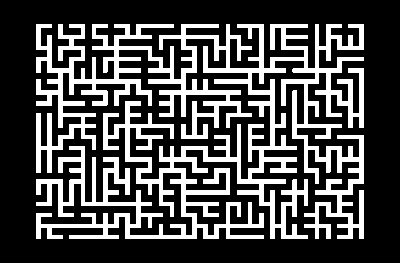

```mathematica
(*custom styling*)style={Background->GrayLevel[0],BaseStyle->{Directive[White,EdgeForm[],Opacity[1]]},VertexShapeFunction->(Rectangle[#1+.16,#1-.16]&),EdgeShapeFunction->(Rectangle[#1[[1]]+.16,#1[[2]]-.16]&)};
embedding=GraphEmbedding[GridGraph[{20,30}]];

g=GridGraph[{20,30},EdgeWeight->RandomReal[10,1150]];
tree=FindSpanningTree[{g,1}];
maze=Graph[tree,VertexCoordinates->embedding,style]
HighlightGraph[maze,PathGraph[FindShortestPath[maze,1,600]]]
```

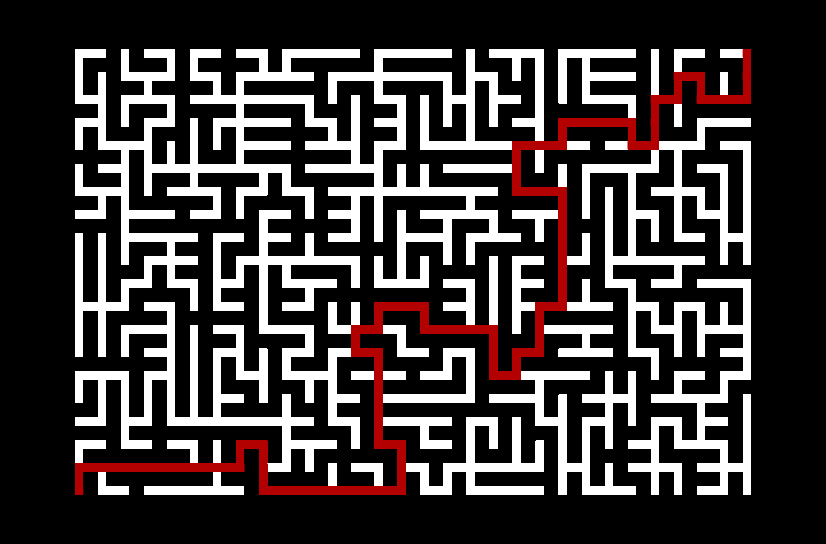

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
color[cycles_]:={cycles,cycles[[All,1]],Style[cycles[[-1,2]],Yellow]}
Dynamic[HighlightGraph[g,color[cycle[[1;;Clock[{1,Length[cycle],1},40]]]]]]
```

{{1<->3,3<->7,7<->11,11<->6,6<->10,10<->14,14<->17,17<->15,15<->18,18<->20,20<->22,22<->21,21<->19,19<->16,16<->12,12<->8,8<->13,13<->9,9<->5,5<->2,2<->4,4<->1}}

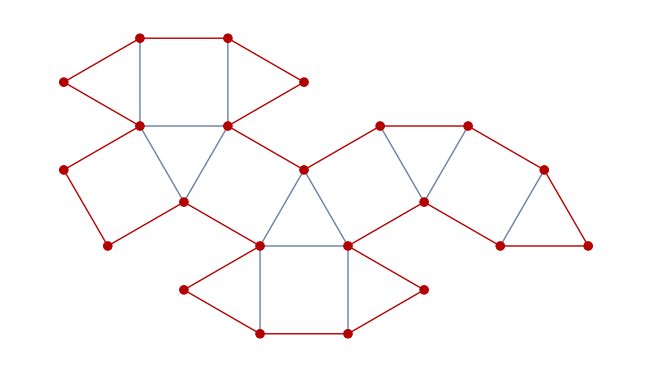

Graphic3D[Cuboctahedron]

```mathematica
g=PolyhedronData["Cuboctahedron","NetGraph"];
FindHamiltonianCycle[g]
HighlightGraph[g,PathGraph[First[%]]]
Graphic3D["Cuboctahedron"]
```

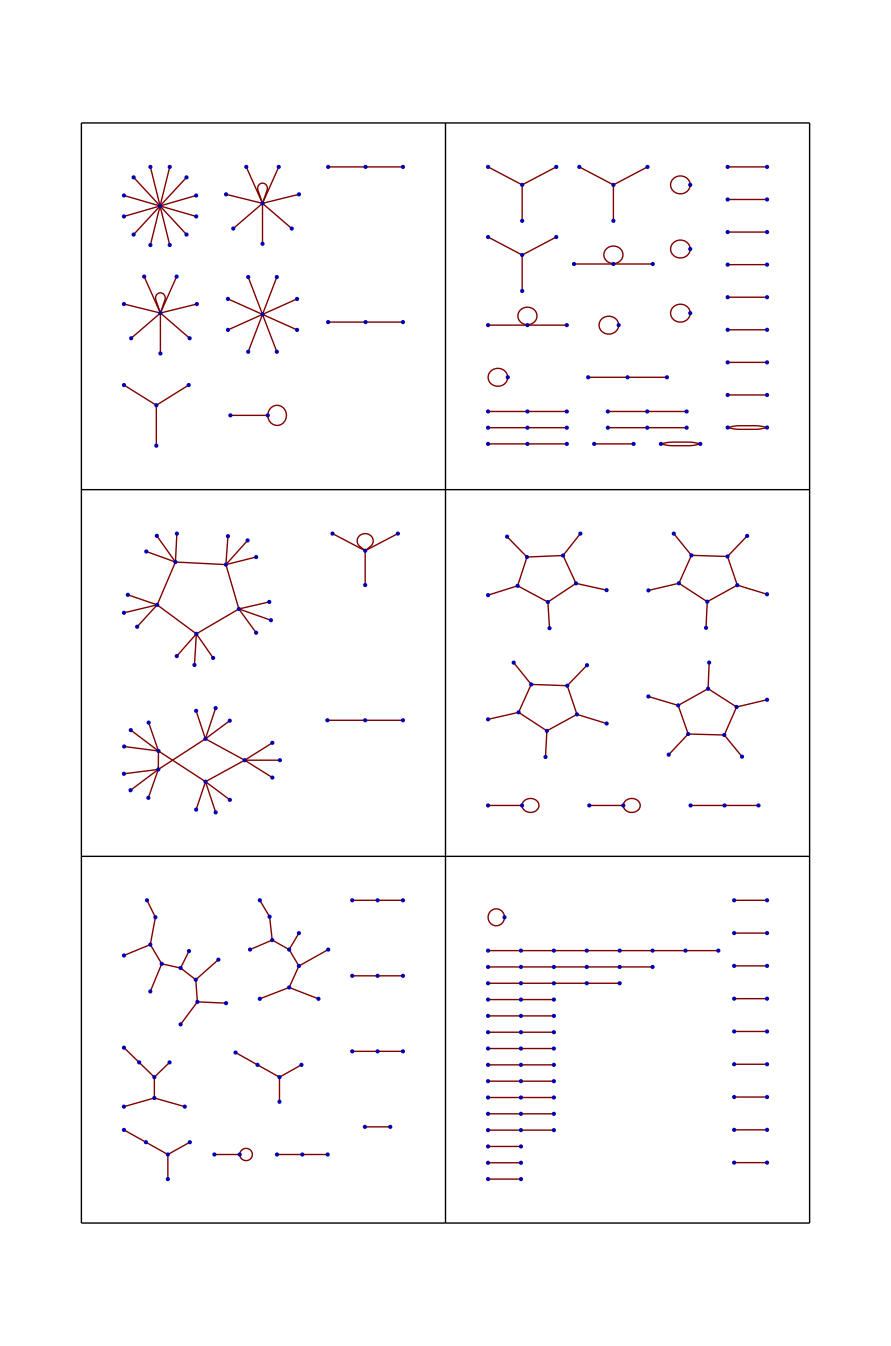

```mathematica
GraphicsGrid[Table[GraphPlot[Table[i->Mod[i^p,m /2 ],{i,m}]],{m,45,47},{p,4,5}],Frame->All]
```

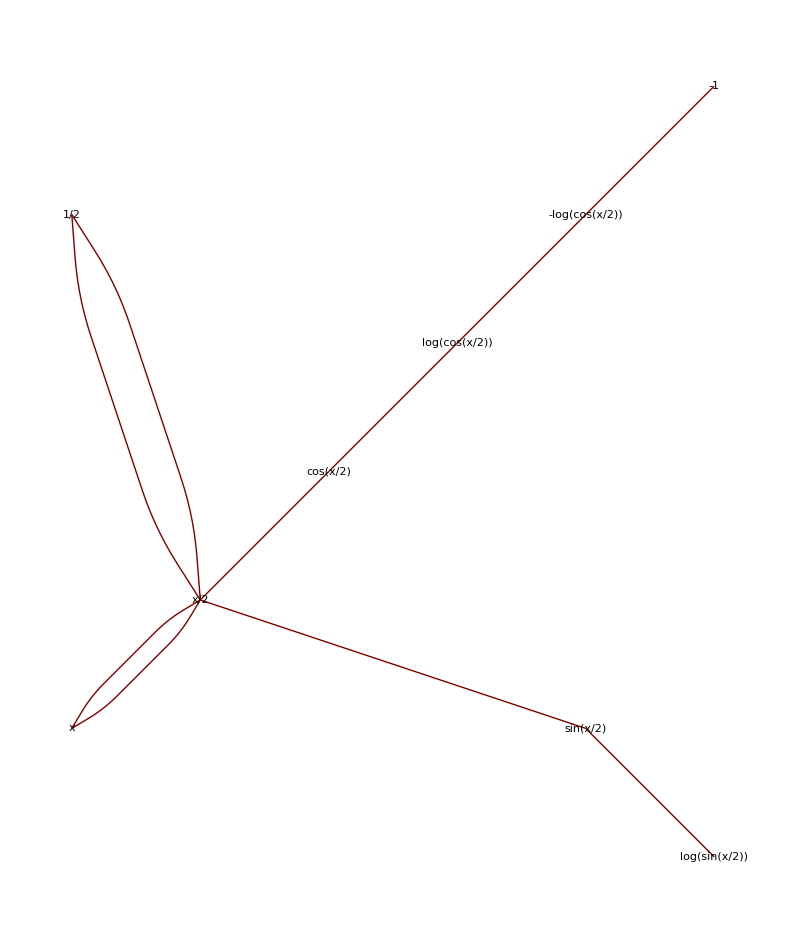

```mathematica
GraphPlot[Flatten[Thread[#->(List@@#)]&/@Level[Integrate[1/Sin[x],x],Infinity]],SelfLoopStyle->None,VertexLabeling->True]
```

```mathematica
words=DictionaryLookup["wol*"]
Flatten[Map[(Thread[#->DeleteCases[Nearest[words,#,3],#]])&,words]];GraphPlot[%,EdgeRenderingFunction->Automatic,VertexRenderingFunction->(Text[#2,#1,Background->White]&)]
```

{wold,wolds,wolf,wolfed,wolfhound,wolfhounds,wolfing,wolfish,wolfishly,wolfram,wolfs,wolverine,wolverines,wolves}

GraphPlot::grph: {wold,wolds,wolf,wolfed,wolfhound,wolfhounds,wolfing,wolfish,wolfishly,wolfram,wolfs,wolverine,wolverines,wolves} is not a valid graph.

GraphPlot[{wold,wolds,wolf,wolfed,wolfhound,wolfhounds,wolfing,wolfish,wolfishly,wolfram,wolfs,wolverine,wolverines,wolves},EdgeRenderingFunction→Automatic,VertexRenderingFunction→(Text[#2,#1,Background→White]&)]

```mathematica
words=DictionaryLookup["*data*"]
```

{data,database,databased,databases,databasing,datable,updatability}

```mathematica
Flatten[Map[(Thread[#->DeleteCases[Nearest[words,#,3],#]])&,words]]
```

{data→datable,data→database,database→databased,database→databases,databased→database,databased→databases,databases→database,databases→databased,databasing→database,databasing→databased,datable→database,datable→data,updatability→databasing,updatability→datable}

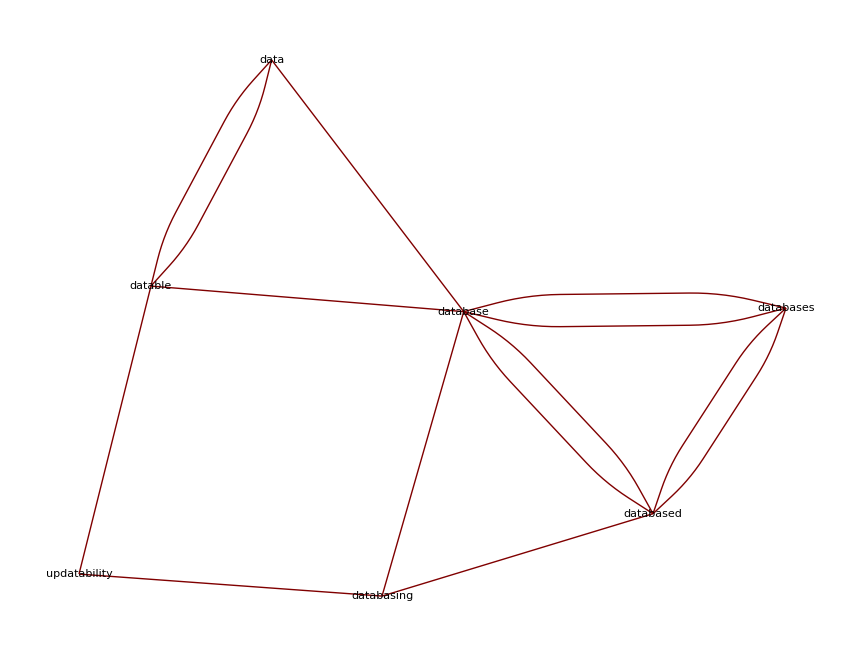

```mathematica
GraphPlot[%,EdgeRenderingFunction->Automatic,VertexRenderingFunction->(Text[#2,#1,Background->White]&)]
```